# 1. kviz - Računalniška orodja v matematiki

Na kvizu je skupno možno doseči 20 točk. Za vsako pravilno rešeno podnalogo dobite 1 točko. Delnih točk ni.
Rešitve pišite takoj pod navodilom ustrezne podnaloge. 

Veliko uspeha pri reševanju!

#### 1. Prepisovalna pravila

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja s klicem funkcije f na argumentu x.

```mathematica
prepis ={  x->f[x]} ;(* imamo x in /. prepiše x v f[x]*)
```

b. Na izrazu `izraz` najprej uporabite pravilo definirano v prejšnji nalogi za funkcijo , nato pa s prepisovalnimi pravili izračunajte vrednost dobljenega izraza za x = e (x = ⅇ) in y = 1/2.

```mathematica
f[x_]:= x^4+1
```

```mathematica
izraz = Log[x] + 2y / x;
```

```mathematica
izraz /.prepis
```

(2 y)/(1+x^4)+Log[1+x^4]

```mathematica
izraz/.{x->E,y->1/2}
```

1+1/ⅇ

c. Definirajte prepisovalno pravilo, ki zamenja vse pojavitve  z .

```mathematica
prepisc = {x^n_ ->Divide[x^(n+1),2n+1]};
```

```mathematica
prepisc
```

{x^n→x^(1+n)/(1+2 n)}

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:=x^(-42)
```

```mathematica
g[x]/.prepisc
```

-1/(83 x^41)

1/(.08x)^42

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`.

```mathematica
Fib[0]=0;
```

```mathematica
Fib[1]=1;
```

```mathematica
Fib[n_] := Fib [n-2]+Fib[n-1]
```

```mathematica
Fib[10]
```

55

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll[Fib,g,f,prepis,prepisc,izraz]
```

b. Definirajte tabelo, ki bo vsebovala numerične približke naravnega logaritma v vseh številih med 1 in 100.

```mathematica
tabelaLog =Table[N[Log10[i]], {i,1,100}]
```

{0.,0.30103,0.477121,0.60206,0.69897,0.778151,0.845098,0.90309,0.954243,1.,1.04139,1.07918,1.11394,1.14613,1.17609,1.20412,1.23045,1.25527,1.27875,1.30103,1.32222,1.34242,1.36173,1.38021,1.39794,1.41497,1.43136,1.44716,1.4624,1.47712,1.49136,1.50515,1.51851,1.53148,1.54407,1.5563,1.5682,1.57978,1.59106,1.60206,1.61278,1.62325,1.63347,1.64345,1.65321,1.66276,1.6721,1.68124,1.6902,1.69897,1.70757,1.716,1.72428,1.73239,1.74036,1.74819,1.75587,1.76343,1.77085,1.77815,1.78533,1.79239,1.79934,1.80618,1.81291,1.81954,1.82607,1.83251,1.83885,1.8451,1.85126,1.85733,1.86332,1.86923,1.87506,1.88081,1.88649,1.89209,1.89763,1.90309,1.90849,1.91381,1.91908,1.92428,1.92942,1.9345,1.93952,1.94448,1.94939,1.95424,1.95904,1.96379,1.96848,1.97313,1.97772,1.98227,1.98677,1.99123,1.99564,2.}

c.  Iz tabele v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu desetin (prvo decimalno mesto) praštevilo.

```mathematica
praDesetina = Select[tabelaLog,PrimeQ[Floor[(#-Floor[#])*10]]&]
```

{0.30103,0.778151,1.20412,1.23045,1.25527,1.27875,1.30103,1.32222,1.34242,1.36173,1.38021,1.39794,1.50515,1.51851,1.53148,1.54407,1.5563,1.5682,1.57978,1.59106,1.70757,1.716,1.72428,1.73239,1.74036,1.74819,1.75587,1.76343,1.77085,1.77815,1.78533,1.79239,1.79934}

6

d. Definirajte anonimno funkcijo enega argumenta, ki  izračuna kub argumenta in prišteje argument in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
j[x_] := x^3+x
```

```mathematica
jseznam = j[praDesetina]
```

{0.328309,1.24934,2.94998,3.09335,3.23322,3.36979,3.50326,3.63381,3.7616,3.88678,4.00949,4.12985,4.91503,5.02003,5.12345,5.22535,5.32579,5.42481,5.52248,5.61882,6.6865,6.76906,6.85077,6.93163,7.01168,7.09093,7.16941,7.24712,7.3241,7.40035,7.47589,7.55075,7.62493}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so soda.

{0,2,4,4,4,6,6,6,6}

```mathematica
Total[Select[Floor[jseznam],Mod[#,2]==0&]]
```

38

#### 3. Analiza z mathematico

a. Definirajte funkcijo .

```mathematica
f[x_]:=5*(E^x)*(x^2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x],x]
```

True

```mathematica
(*x je katerokoli realno število*)
```

c. Izračunajte zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x],x,y]
```

y≥0

d. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x],x->Infinity]
```

∞

```mathematica
Limit[f[x],x->-Infinity]
```

0

e. Izračunajte odvod funkcije .

```mathematica
odvod =D[f[x],x]
```

10 ⅇ^x x+5 ⅇ^x x^2

f. Izračunajte lokalne ekstreme funkcije  (določi tudi ali gre za lokalni minimum oz. maksimum).

```mathematica
Map[{#, f[#]}&, Solve[odvod == 0, x] // Flatten // Values]
```

{{-2,20/ⅇ^2},{0,0}}

g. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[odvod>=0,x] (*narašča*)
```

x≤-2||x≥0

```mathematica
Reduce[odvod<=0,x](*pada*)
```

-2≤x≤0

h. Narišite graf funkcije  na intervalu [-1, 2].

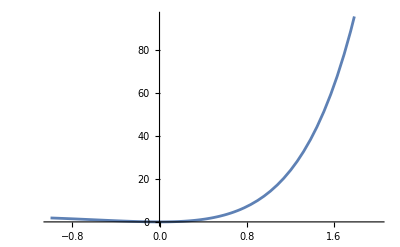

```mathematica
Plot[f[x],{x,-1,2}]
```

i. Določite intervale konveksnosti in konkavnosti funkcije .

```mathematica
odvod2 = D[odvod,x]
```

10 ⅇ^x+20 ⅇ^x x+5 ⅇ^x x^2

```mathematica
Reduce[odvod2 >= 0, x] (* konveksno *)
Reduce[odvod2 <= 0, x] (* konkavno *)
```

x≤-2-√2||x≥-2+√2

-2-√2≤x≤-2+√2

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [-3, 0]. Vrtenino tudi narišite.

```mathematica
Plot[Integrate[f,x],{x,-3,0}]
```

Integrate::ilim: Invalid integration variable or limit(s) in -2.99994.

Integrate::ilim: Invalid integration variable or limit(s) in -2.93871.

Integrate::ilim: Invalid integration variable or limit(s) in -2.87749.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-